{{17/6,-10/3,1/2},{-10/3,8,-14/3},{1/2,-14/3,25/6}}

(1 | 0 | 0
-10/3 | 8 | -14/3
1/2 | -14/3 | 25/6)

{1.,-1.38846,-2.32308}

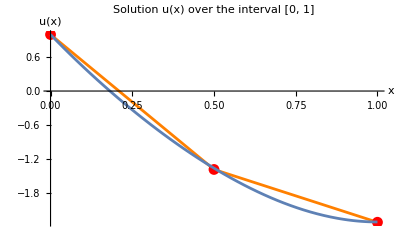

```mathematica
n=1; 
s =2;
nodes=Table[i/n,{i,0,n}]; 
a[x_]:=1+x;
f[x_]:=-18 x^2; 
LagrangeBasis[i_,x_, nodes_]:=Product[(x-nodes[[j]])/(nodes[[i]]-nodes[[j]]),{j,DeleteCases[Range[1,s+1],i]}];
Ke[nodes_]:=Table[Integrate[a[x]*D[LagrangeBasis[i,x,nodes],x]* D[LagrangeBasis[j,x,nodes],x],{x,nodes[[1]],nodes[[s+1]]}],{i,1,s+1},{j,1,s+1}];
fe[nodes_]:=Table[Integrate[f[x]*LagrangeBasis[i,x,nodes],{x,nodes[[1]],nodes[[s+1]]}],{i,1,s+1}];
globalKe=ConstantArray[0,{(n*s)+1,(n*s)+1}];
globalFe=ConstantArray[0,(n*s)+1];
For[e=1, e<=n, e++,
mainNodes={nodes[[e]],nodes[[e+1]]};
Print[Ke[elementNodes]];
elementNodes=Table[mainNodes[[1]]+(mainNodes[[2]]-mainNodes[[1]])*(i/s),{i,0,s}];
globalIndices=Range[(e-1)*s+1,e*s+1];
globalKe[[globalIndices,globalIndices]]+=Ke[elementNodes];
globalFe[[globalIndices]]+=fe[elementNodes];]
globalKe[[1,1]]=1;
globalKe[[1,2;;]]=0;
globalFe[[1]]=1;

u=LinearSolve[globalKe,globalFe];
Table[i/(n*s),{i, 0,n*s}];
plotu =ListLinePlot[Transpose[{Table[i/(n*s),{i, 0,n*s}],u}],PlotRange->All,PlotLabel->"Solution u(x) over the interval [0, 1]",AxesLabel->{"x","u(x)"},PlotStyle->Orange,PlotStyle->Thick,Mesh->All,MeshStyle->Red];
deqn=-D[(1+x) D[c[x],x],x]==-18 x^2;
bc={c[0]==1,{D[c[x],x]/. x->1}==0};
exactSolution=DSolve[{deqn,bc},c[x],x];
realresult[p_] = c[x] /.exactSolution[[1]]; 
plotreal = Plot[realresult[x], {x, 0,1}];
globalKe //MatrixForm
u //N
Show[plotu, plotreal]
```